```mathematica
Grid[{{-Graphics-,"Anno Accademico 2017/18"}},ItemStyle->{Automatic,{1->{FontFamily->"Roboto Condensed",FontSize->20}}},Frame-> True,FrameStyle->{RGBColor[0.94,0.94,0.94]},Alignment->{{Left,Right}},Spacings->10,ItemSize-> Fit]
```

-Graphics- | Anno Accademico 2017/18

```mathematica
Grid[{{"Sistemi Lineari e Metodo di Gauss"}},ItemSize->Fit,Frame->True, FrameStyle->{RGBColor[0.13,0.52,0.96]},Spacings->{5,7},Background->{RGBColor[0.84,0.93,0.98]},ItemStyle->{Automatic, {1-> {FontFamily-> "Roboto Condensed", FontSize->40, FontColor->RGBColor[0.13,0.52,0.96]}}}]
```

Sistemi Lineari e Metodo di Gauss

```mathematica
Grid[{{-Graphics-, Column[{Style["Progetto D'Esame:", Red],"Matematica Computazionale (LM Informatica)\nCalcolo Numerico e Software Didattico (LM Matematica)","Sara Annese\nLaura Cappelli\nMatteo Del Vecchio\nMatteo Marchesini\nDaniele Rossi\nSilvia Scibilia"},Frame->None,Spacings->1]}}, ItemSize->Fit, Frame->None, Alignment->{{Right, Left}},Spacings->3, ItemStyle->{Automatic, {1-> {FontFamily->"Roboto Condensed", FontSize-> 18}}}]
```

-Graphics- | Progetto D'Esame:
Matematica Computazionale (LM Informatica)
Calcolo Numerico e Software Didattico (LM Matematica)
Sara Annese
Laura Cappelli
Matteo Del Vecchio
Matteo Marchesini
Daniele Rossi
Silvia Scibilia

```mathematica
forwardTag = "ReadySetGoTitle";
forwardButton := Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb",forwardTag}];
forwardLink := Hyperlink["Avanti", {"Home.nb", forwardTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvanti := Grid[{{forwardLink,forwardButton}},Alignment->{Right}, ItemSize->{{Scaled[0.93],Scaled[0.07]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvanti
Clear[forwardTag];
```

AvantiHome.nbReadySetGoTitleHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbReadySetGoTitleHome.nb

### Ready, Set, Go!

#### 1. Clicca sul pulsante in basso per caricare il package necessario

```mathematica
loadPackageButton = Button[Style["Carica Package!", FontSize->30, RGBColor[0.13,0.52,0.96]],
	SetDirectory[NotebookDirectory[]]; Get["GaussLinearSystemsPackage.m"];
	MessageDialog["Il package è stato caricato correttamente!"]
];Grid[{{loadPackageButton}},ItemSize->Fit, Frame->True, FrameStyle->{RGBColor[0.94,0.94,0.94]}, Spacings->{40,0}]
```

Carica Package!

#### 2. Valutazione delle celle

Mettere qui foto/gif/video di come fare la valutazione delle celle di inizializzazione

```mathematica
backTag = "Homepage";
forwardTag = "BlackboardHeader";
backButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb",backTag}];
backLink := Hyperlink["Indietro", {"Home.nb", backTag},BaseStyle->RGBColor[0.2,0.6,0.86]];

navAvantiIndietro := Grid[{{backButton,backLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.42],Scaled[0.42],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbHomepageHome.nb | IndietroHome.nbHomepageHome.nbHyperlinkHyperlinkActive | AvantiHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb

### Clicca su un argomento per iniziare...

```mathematica
buttonSistemi = Hyperlink[Button[-Graphics- , Background->White],{"Home.nb", "SistemiLineari"}];
buttonMatrici = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "MatriciPag1"}];
buttonGauss = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Gauss"}];
buttonEsercizi = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Esercizi"}];
SetDirectory[NotebookDirectory[]];
blackboard = Import["images/blackboardText.jpg"];
grid = Grid[{{buttonSistemi, buttonMatrici},{buttonGauss, buttonEsercizi}}];
Overlay[{blackboard,grid},All,2,Alignment->Center]
```

-Graphics--Graphics-Home.nbSistemiLineariHome.nb | -Graphics-Home.nbMatriciPag1Home.nb
-Graphics-Home.nbGaussHome.nb | -Graphics-Home.nbEserciziHome.nb

### Dai sistemi lineari...

#### Nozioni fondamentali

```mathematica
firstPart = "Un sistema lineare è un sistema costituito da equazioni in cui le ";
styledPart = "incognite";
lastPart = " compaiono al primo grado.";
styledString = {firstPart, Style[styledPart, Red], lastPart};
styledString = Apply[StringJoin, ToString[#, StandardForm] & /@ styledString];
Grid[{{styledString}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
Spacer[5]
styledString2 = {"Le lettere x, y, z rappresentano le ", Style["incognite", Red], " del sistema.\nI termini a, b, c sono detti ", Style["coefficienti", RGBColor[0.13,0.52,0.96]], " e gli altri elementi sono chiamati ", Style["termini noti", RGBColor[0.14,0.61,0.14]]};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
Spacer[10]
genericSystem = Image[Import["images/generic-system.png"],Magnification->0.3];
exampleSystem = Image[Import["images/example-system.png"], Magnification->0.3];
Grid[{{genericSystem,"ESEMPIO\n⟹" ,exampleSystem}}, Frame->None, ItemSize->Fit, Spacings->{1,2}, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize -> 30, TextAlignment->Center], Alignment->{{Right, Center, Left}}]
```

Un sistema lineare è un sistema costituito da equazioni in cui le incognite compaiono al primo grado.

Le lettere x, y, z rappresentano le incognite del sistema.
I termini a, b, c sono detti coefficienti e gli altri elementi sono chiamati termini noti

-Graphics- | ESEMPIO
⟹ | -Graphics-

#### Attento! Le incognite sono x, y, z, le altre lettere che compaiono sono tutti numeri. Non confonderti!

```mathematica
forwardTag = "SistemiLineariPag2";
startButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb","BlackboardHeader"}];
startLink = Hyperlink["Torna all'Inizio", {"Home.nb", "BlackboardHeader"},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizio := Grid[{{startButton,startLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.42],Scaled[0.42],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag2Home.nb

### Dai sistemi lineari...

#### I sistemi di equazioni di primo grado: Esempio di un sistema di due equazioni in due incognite

Risolto per via grafica con metodo delle rette su piano cartesiano.

```mathematica
(*eqType1String = "Due equazioni in due incognite";
eqType2String = "Tre equazioni in tre incognite";
eqType3String = {Style["m", Bold], " equazioni in ", Style["n", Bold], " incognite (caso più generale)"};
eqType3String = Apply[StringJoin, ToString[#, StandardForm] & /@ eqType3String];*)

(*rulesIncognite = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;
rulesCoefficienti = <|2->Style["2", RGBColor[0.13,0.52,0.96]],3->Style["3", RGBColor[0.13,0.52,0.96]]|>;
rulesTerminiNoti = <|12->Style["12", RGBColor[0.14,0.61,0.14]],7->Style["7", RGBColor[0.14,0.61,0.14]]|>;*)
(*hightlightRules = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;

eqsType1={Subscript[a,1] x + Subscript[b, 1] y == Subscript[c,1],Subscript[a,2] x + Subscript[b, 2] y == Subscript[c,2]};
eqsType1 = eqsType1 /. hightlightRules;

eqsType2 = {Subscript[a,1] x + Subscript[b, 1] y + Subscript[c,1] z == Subscript[d,1],Subscript[a,2] x + Subscript[b, 2] y + Subscript[c,2] z == Subscript[d,2], Subscript[a,3] x + Subscript[b, 3] y + Subscript[c,3] z == Subscript[d,3]};
eqsType2 = eqsType2 /. hightlightRules;

eqsType3 = {Subscript[a, 11] Subscript[x, "1"] + Subscript[a, 12] Subscript[x, "2"] + Subscript[a, HoldForm[1 n]] Subscript[x, "n"] == Subscript[b, 1],Subscript[a, 21] Subscript[x, "1"] + Subscript[a, 22] Subscript[x, "2"] + Subscript[a, HoldForm[2 n]] Subscript[x, "n"] == Subscript[b, 2],Subscript[a, 31] Subscript[x, "1"] + Subscript[a, 32] Subscript[x, "2"] + Subscript[a, HoldForm[3 n]] Subscript[x, "n"] == Subscript[b, 3],Subscript[a, HoldForm[m 1]] Subscript[x, "1"] + Subscript[a, HoldForm[m 2]] Subscript[x, "2"] + Subscript[a, HoldForm[m n]] Subscript[x, "n"] == Subscript[b, "m"]};
FullForm[eqsType3[[4]]]
eqsType3 = eqsType3 /. hightlightRules;

Grid[{{eqType1String, eqType2String, eqType3String},
{Equations[eqsType1, Alignment->True]//TraditionalForm, Equations[eqsType2, Alignment->True]//TraditionalForm, Equations[eqsType3, Alignment->True]//TraditionalForm}},
Frame->All, ItemSize->Fit, Spacings->{2,2}, ItemStyle->{FontFamily->"Roboto Condensed",{1->Directive[FontSize->20,FontName->"Arial"],2->Directive[FontSize->24]}}]*)
```

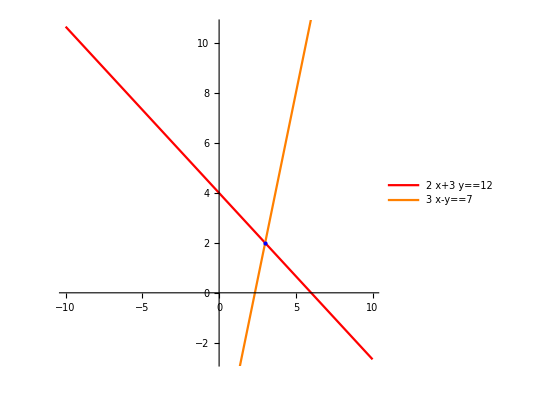
{2 x+3 y==12
3 x-y==7 | ⟹ |  | 2 | x | 3 | y | 12
3 | x | -1 | y | 7
-Graphics- |  |  |

```mathematica
(*rulesIncognite = <|x->Style[x, Red], y->Style[y, Red], z->Style[z, Red]|>;
rulesCoeffPag2 = <|2-> Style["2", RGBColor[0.13,0.52,0.96]],3->Style["3", RGBColor[0.13,0.52,0.96]]|>;
rulesTermPag2 = <|12->Style["12", RGBColor[0.14,0.61,0.14]],7->Style["7", RGBColor[0.14,0.61,0.14]]|>;*)

eqs2x2 = {2x+3y==12, 3x-y== 7};
(*eqs2x2Vis = eqs2x2 /. rulesIncognite /. rulesCoeffPag2 /. rulesTermPag2;*)

redLegend = {"Il colore ", Style["ROSSO", {Bold,Red}], " identifica le ", Style["INCOGNITE", Bold]};
redLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ redLegend];

blueLegend = {"Il colore ", Style["BLU", {Bold,Blue}], " identifica i ", Style["COEFFICIENTI", Bold]};
blueLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ blueLegend];

greenLegend = {"Il colore ", Style["VERDE", {Bold,RGBColor[0.14,0.61,0.14]}], " identifica i ", Style["TERMINI NOTI", Bold]};
greenLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ greenLegend];

legend=SwatchLegend[{Red,RGBColor[0.13,0.52,0.96],RGBColor[0.14,0.61,0.14]},{redLegendString,blueLegendString,greenLegendString}];

Grid[{{displayEquationSystem[eqs2x2],"⟹",SpanFromLeft,highlightElementsTable[eqs2x2]},{plotLinearSystem2[eqs2x2[[1]],eqs2x2[[2]]],SpanFromLeft,legend,SpanFromLeft}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.45],Scaled[0.05],Scaled[0.05],Scaled[0.45]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40,FontSize->20},{1,3}->{Alignment->Left}}]
```

```mathematica
backTag = "SistemiLineari";
forwardTag = "SistemiLineariPag3";
navAvantiInizioIndietro := Grid[{{backButton, backLink, startButton, startLink, forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.25], Scaled[0.08],Scaled[0.25],Scaled[0.25],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariHome.nb | IndietroHome.nbSistemiLineariHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag3Home.nb

### Dai sistemi lineari...

#### I sistemi di equazioni di primo grado: Esempio di sistema di tre equazioni in tre incognite

```mathematica
(*rulesCoeffPag3 = <|2:>(Style["2", RGBColor[0.13,0.52,0.96]]//TraditionalForm),-3:> (Style["-3", RGBColor[0.13,0.52,0.96]]//TraditionalForm)|>;
rulesTermPag3 = <|6:> Style["6", RGBColor[0.14,0.61,0.14]],1:> Style["1", RGBColor[0.14,0.61,0.14]]|>;

rulesRewrite = <|6->"6tn", 1->"1tn", -1->"-1tn"|>;*)

(*eqs3x3Vis = eqs3x3 /. rulesIncognite /. rulesCoeffPag3;
eqs3x3 // FullForm;
eqs3x3 /. rulesIncognite // FullForm;
eqs3x3 /. rulesIncognite /. rulesCoeffPag3 // FullForm;
eqs3x3 /. rulesIncognite /. rulesCoeffPag3 /. rulesTermPag3
eqs3x3 /. {rulesIncognite, rulesCoeffPag3, rulesTermPag3};*)

(*eqs3x3Replaced = eqs3x3 /. rulesRewrite;
result = Level[eqs3x3[[2]], 1];
Level[%[[1]],1];
lhs = Level[eqs3x3[[3]],1][[2]];
variabili = Variables[lhs];
(*CoefficientList[lhs,y]*)
CoefficientRules[lhs,variabili];
Values[%];

For[i=1,i≤Length[eqs3x3],i++,
	(*Print[eqs3x3[[i]]];*)
	termineNoto = Level[eqs3x3[[i]],1][[2]];
	lhs = Level[eqs3x3[[i]],1][[1]];
	variabili = Sort[Variables[lhs]];
	coefRules = CoefficientRules[lhs,variabili];
	Print[coefRules];
	Print[FromCoefficientRules[coefRules, variabili]];
	coefficienti = Values[coefRules];
	For[j=1,j≤Length[coefficienti],j++,coefficienti[[j]] = Style[coefficienti[[j]],RGBColor[0.13,0.52,0.96]]];
	For[j=1,j≤Length[variabili],j++,variabili[[j]] = Style[variabili[[j]],RGBColor[1.0,0,0]]];
	termineNoto = Style[termineNoto, RGBColor[0.14,0.61,0.14]];
	flattened = Flatten[{coefficienti,variabili,termineNoto}];
	Print[flattened];
]*)
eqs3x3 = {x+y+z==6,2x+y-z==1,2x-3y+z==-1};
Grid[{{displayEquationSystem[eqs3x3],"⟹",SpanFromLeft,highlightElementsTable[eqs3x3]},{plotLinearSystem3[eqs3x3[[1]],eqs3x3[[2]],eqs3x3[[3]]], SpanFromLeft,legend,SpanFromLeft}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.45],Scaled[0.05],Scaled[0.05],Scaled[0.45]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40,FontSize->20},{1,3}->{Alignment->Left}}]
```

{x+y+z==6
2 x+y-z==1
2 x-3 y+z==-1 | ⟹ |  | 1 | x | 1 | y | 1 | z | 6
2 | x | 1 | y | -1 | z | 1
2 | x | -3 | y | 1 | z | -1
-Graphics3D- |  |  |

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb","BlackboardHeader"}];
forwardButton = Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb","Risoluzione"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}];*)

backTag = "SistemiLineariPag2";
forwardTag = "Risoluzione";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariPag2Home.nb | IndietroHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbRisoluzioneHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbRisoluzioneHome.nb

### Dai sistemi lineari...

#### Risoluzione

```mathematica
myString1= "Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.\nProsegui al ";

nextChapterButton = Hyperlink[Button[Style["prossimo capitolo", FontFamily-> "Roboto Condensed", FontSize-> 24, RGBColor[0.13,0.52,0.96], Bold], Appearance-> {None}],{"Home.nb", "BlackboardHeader"}];
myString2 =" per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.\nÈ un metodo generale che, come vedremo, include casi particolari come quelli che già conosci";
myString3 = {myString1,nextChapterButton,myString2};
myString3 = Apply[StringJoin, ToString[#, StandardForm]& /@ myString3];
Grid[{{myString3}}, Frame -> None, Alignment->{{Left, Right}},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left] ]
```

Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.
Prosegui al prossimo capitolo per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.
È un metodo generale che, come vedremo, include casi particolari come quelli che già conosci

```mathematica
navInizio := Grid[{{startButton,startLink}},Alignment->{Left}, ItemSize->{{Scaled[0.07],Scaled[0.93]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navInizio
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive

### ... alle Matrici

```mathematica
styledString2 ={"È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono: i coefficienti e i termini noti del sistema.\nQuesta è detta ", Style["MATRICE COMPLETA", Red], ". ", Style["I coefficienti devono essere ordinati.", Underlined],"\n\nGuarda i colori per comprendere il posizionamento dei numeri"};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]

linearSystem1 = {7x+6y+5z==-5, 3x-4y+2z==1, -5x+6y-4z == 1};
matrixForm1= highlightMatrixElements[transformToMatrix[linearSystem1,True]]//MatrixForm;

linearSystem2= {7x+6y+5z==0,-4y+2z ==1,5x+6y==1};
matrixForm2 = highlightMatrixElements[transformToMatrix[linearSystem2,True]]//MatrixForm;

Grid[{{displayEquationSystem[linearSystem1],"⟹",matrixForm1},{displayEquationSystem[linearSystem2],"⟹",matrixForm2}},Frame -> None, ItemSize->Fit, Spacings->{1, 2}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
Spacer[20]
```

È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono: i coefficienti e i termini noti del sistema.
Questa è detta MATRICE COMPLETA. I coefficienti devono essere ordinati.

Guarda i colori per comprendere il posizionamento dei numeri

{7 x+6 y+5 z==-5
3 x-4 y+2 z==1
-5 x+6 y-4 z==1 | ⟹ | (7 | 6 | 5 | -5
3 | -4 | 2 | 1
-5 | 6 | -4 | 1)
{7 x+6 y+5 z==0
-4 y+2 z==1
5 x+6 y==1 | ⟹ | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 6 | 0 | 1)

#### Attenzione ! Se nel sistema non compare un’incognita, nella matrice al posto corrispondente bisogna mettere uno 0 (zero).

```mathematica
(*exerciseButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb", "BlackboardHeader"}];
forwardButton = Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb","MatriciPag2"}];Grid[{{exerciseButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}];*)

forwardTag = "MatriciPag2";
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag2Home.nb

### Matrici

#### Definizione informale di matrice

```mathematica
matrixElement = Subscript[a, HoldForm["i""j"]];
matrix ={{Subscript[a, HoldForm["1"1]], Subscript[a, HoldForm["1"2]], …, Subscript[a, HoldForm["1""m"]]}, {Subscript[a, HoldForm["2"1]], Subscript[a, HoldForm["2"2]], …, Subscript[a, HoldForm["2""m"]]}, {⋮, ⋮, ⋱, ⋮}, {Subscript[a, HoldForm["n"1]], Subscript[a, HoldForm["n"2]], …, Subscript[a, HoldForm["n""m"]]}} // MatrixForm;matrixRule = <| "1"-> Style[matrix[[1,1,1,2,1]], RGBColor[0.13,0.52,0.96]], 1-> Style[matrix[[1,1,1,2,1]], Red], 2 -> Style[matrix[[1,2,1,2,1]], Red], "2" -> Style[matrix[[1,2,1,2,1]],RGBColor[0.13,0.52,0.96]], "m" -> Style[matrix[[1,1,4,2,1,2]], Red], "n" -> Style[matrix[[1,4,1,2,1]], RGBColor[0.13,0.52,0.96]]|>;
matrixElementRule = <| "i" ->  Style[matrixElement[[2,1,1]], RGBColor[0.13,0.52,0.96]], "j" -> Style[matrixElement[[2,1,2]], Red]|>;
myMatrix = matrix /. matrixRule;
myMatrixElement = matrixElement /. matrixElementRule;
stringMatrix = {"matrice ", Style["n", RGBColor[0.13,0.52,0.96]], " x ",  Style["m", Red]};
stringMatrix = Apply[StringJoin, ToString[#, StandardForm]& /@ stringMatrix];
columns= -Graphics-;
rows = -Graphics-;
(*Grid[{{"Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne."},{Framed[Grid[{{Framed[myMatrixElement, FrameMargins-> {{20,0}, {0, 0}},FrameStyle -> None], columns}, {rows, myMatrix}, {Framed[stringMatrix, FrameMargins-> {{85,0}, {0, 0}},FrameStyle -> None], SpanFromLeft }}, Frame -> None, ItemStyle ->Directive[FontFamily->"Roboto Condensed",FontSize -> 30]], FrameMargins-> {{0,0}, {0,30}}, FrameStyle-> None]}}, ItemSize->Fit]*)

Grid[{{"Una matrice è una tabella ordinata di elementi disposti su " <> ToString[Style["n", RGBColor[0.13,0.52,0.96]],StandardForm] <> " righe e " <> ToString[Style["m", Red],StandardForm] <> " colonne."},{
Grid[{{myMatrixElement,columns},{rows,myMatrix},{stringMatrix,SpanFromLeft}},Frame->None]
}}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28], ItemSize->Fit, Frame->None]

Spacer[20]

Grid[{{"Al suo interno possono comparire numeri positivi, negativi o anche zeri."}},Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28, TextAlignment->Center]]
```

Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne.
a_(i j) | -Graphics-
-Graphics- | (a_(1 1) | a_(1 2) | … | a_(1 m)
a_(2 1) | a_(2 2) | … | a_(2 m)
⋮ | ⋮ | ⋱ | ⋮
a_(n 1) | a_(n 2) | … | a_(n m))
matrice n x m |

Al suo interno possono comparire numeri positivi, negativi o anche zeri.

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag1"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag3"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag1";
forwardTag = "MatriciPag3";
exerciseTag = "TAGQUI";
exerciseButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb", exerciseTag}];
exerciseLink := Hyperlink["Prova tu!", {"Home.nb", exerciseTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizioEserciziIndietro := Grid[{{backButton, backLink, startButton, startLink, exerciseButton, exerciseLink, forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Left, Right, Left, Right, Right}}, ItemSize->{{Scaled[0.09],Scaled[0.15], Scaled[0.09],Scaled[0.22],Scaled[0.09],Scaled[0.15],Scaled[0.1],Scaled[0.09]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioEserciziIndietro
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbMatriciPag1Home.nb | IndietroHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbTAGQUIHome.nb | Prova tu!Home.nbTAGQUIHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag3Home.nb

### Matrici

#### Elemento di una matrice

```mathematica
matrixPhrase="Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.";

tableMatrix =Grid[
Table[
{
{"", Rotate[" 1.aa Colonna", Pi/2],Rotate[" 2.aa Colonna", Pi/2],Rotate[" 3.aa Colonna", Pi/2],Rotate[" 4.aa Colonna", Pi/2]},
{"1.aa riga",7,6,5,0},
{"2.aa riga",0,-4,2,1},
{"3.aa riga",5,Item[7, Frame-> True, FrameStyle->Directive[Yellow, Thickness-> Large]],0,1}}
],
Dividers->{{None,Black,None,None,None,Black},{None, Black, None, None, Black}}, Background->{Automatic,Automatic,{{{4,4},{2,5}}->Red,{{2,4},{3,3}}->Blue}}, ItemStyle->{Automatic,Automatic,{{2,4},{3,3}}->{FontColor->White}}];
exampleImage = -Graphics-;
Grid[{{matrixPhrase},{tableMatrix}, {exampleImage}}, Frame -> None, ItemSize->Scaled[1], Spacings->{3, 3},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.
 |  1.aa Colonna |  2.aa Colonna |  3.aa Colonna |  4.aa Colonna
1.aa riga | 7 | 6 | 5 | 0
2.aa riga | 0 | -4 | 2 | 1
3.aa riga | 5 | 7 | 0 | 1
-Graphics-

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag2"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag4"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag2";
forwardTag = "MatriciPag4";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag2Home.nb | IndietroHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag4Home.nb

### Matrici

#### Tipologia di matrici

```mathematica
firstStringSquaredMatrix = {Style["Matrice quadrata\n", Bold], "numero di righe = numero di colonne"};
firstStringSquaredMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringSquaredMatrix];
firstStringRectangularMatrix = {Style["Matrice rettangolare\n", Bold], Style["numero di righe ≠ numero di colonne", FontFamily-> "Roboto Condensed", FontSize-> 24]};
firstStringRectangularMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringRectangularMatrix];
squaredMatrix = {{4, 3, 7, 9, -1}, {7, 1, 0, 6, 5}, {1, 6, 3, -4, 5}, {0, -7, 0, -9, 2}, {5, -1, -1, 7, 0}} // MatrixForm;
rectangularMatrix = {{7, 6, 5, 0}, {0, -4, 2, 1}, {5, 7, 0, 1}} // MatrixForm;
secondStringSquaredMatrix = Style["Matrice 5 x 5", Italic];
secondStringRectangularMatrix = Style["Matrice 3 x 4", Italic];

Grid[{{firstStringSquaredMatrix,firstStringRectangularMatrix}, {squaredMatrix, rectangularMatrix}, {secondStringSquaredMatrix, secondStringRectangularMatrix}}, Frame-> None, Spacings-> {1,1}, ItemSize-> Fit ,ItemStyle-> Directive[TextAlignment -> Center, FontFamily -> "Roboto Condensed", FontSize -> 24]]
```

Matrice quadrata
numero di righe = numero di colonne | Matrice rettangolare
numero di righe ≠ numero di colonne
(4 | 3 | 7 | 9 | -1
7 | 1 | 0 | 6 | 5
1 | 6 | 3 | -4 | 5
0 | -7 | 0 | -9 | 2
5 | -1 | -1 | 7 | 0) | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 0 | 1)
Matrice 5 x 5 | Matrice 3 x 4

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag3"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag5"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag3";
forwardTag = "MatriciPag5";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag3Home.nb | IndietroHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag5Home.nb

### Matrici

#### Diagonale di una matrice

```mathematica
firstString = "La " <> ToString[Style["diagonale", Bold], StandardForm] <> " di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.\nSono quelli evidenziati in " <> ToString[Style["rosso", Red], StandardForm] <> ".";
secondString = {Style["Attenzione!\n", Red, Bold], "Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {5, 7, Style[0, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {5, 7, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

Grid[{{firstString}, {squaredMatrix}, {secondString}, {rectangularMatrix}}, Frame -> None, Spacings-> {0,2}, ItemSize-> Fit, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

La diagonale di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.
Sono quelli evidenziati in rosso.
(7 | 6 | 5
0 | -4 | 2
5 | 7 | 0)
Attenzione!
Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari.
(7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 3 | 1)

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag4"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag6"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag4";
forwardTag = "MatriciPag6";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag4Home.nb | IndietroHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag6Home.nb

### Matrici

#### Matrice triangolare e a gradini

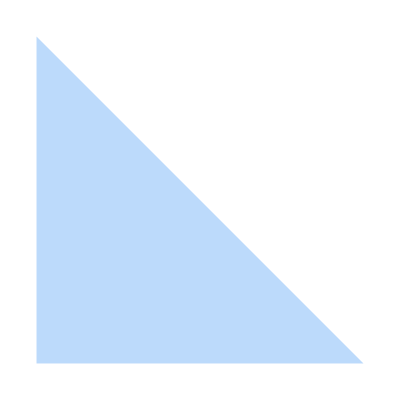
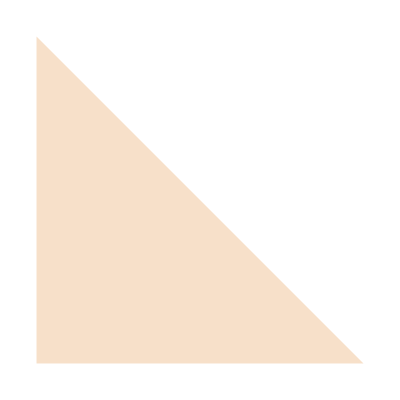
Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di matrice triangolare superiore.
-Graphics-(7 | 6 | 5
0 | -4 | 2
0 | 0 | 9)
Una matrice rettangolare a gradini presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo pivot.
-Graphics-(7 | 6 | 5 | 0
0 | -4 | 2 | 1
0 | 0 | 3 | 1)

```mathematica
firstString = {"Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di ", Style["matrice triangolare superiore", Bold], "."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"Una ", Style["matrice rettangolare a gradini", Bold], " presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo ", Style["pivot",  RGBColor[0.2, 0.6, 0.2], Bold], "."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {0, 0, Style[9, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {0, 0, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

triangle = Triangle[{{0,0}, {0,1}, {1,0}}];
triangleGridSquaredMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
triangleGridRectagularMatrix = Grid[{{Graphics[{RGBColor[0.9,0.60,0.30, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
upperTriangularMatrix = Overlay[{triangleGridSquaredMatrix, squaredMatrix},All, 2];
rectangularSteppedMatrix = Overlay[{triangleGridRectagularMatrix, rectangularMatrix},All, 2];

Grid[{{firstString}, {upperTriangularMatrix}, {secondString}, {rectangularSteppedMatrix}}, Frame -> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag5"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag7"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag5";
forwardTag = "MatriciPag7";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag5Home.nb | IndietroHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag7Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag7Home.nb

### Matrici

#### Matrice diagonale e matrice identità

```mathematica
firstString = {"Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama ", Style["matrice diagonale", Bold],"."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"La matrice diagonale che presenta solo 1 sulla diagonale si chiama ", Style["matrice identità", Bold],"."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

diagonalMatrix = {{Style[7, Red], 0, 0}, {0, Style[-4, Red], 0}, {0, 0, Style[9, Red]}} // MatrixForm;
identityMatrix = {{Style[1, Red], 0, 0}, {0, Style[1, Red], 0}, {0, 0, Style[1, Red]}} // MatrixForm;

Grid[{{firstString}, {diagonalMatrix}, {secondString}, {identityMatrix}}, Frame-> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama matrice diagonale.
(7 | 0 | 0
0 | -4 | 0
0 | 0 | 9)
La matrice diagonale che presenta solo 1 sulla diagonale si chiama matrice identità.
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag6"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag8"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag6";
forwardTag = "MatriciPag8";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag6Home.nb | IndietroHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag8Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag8Home.nb

### Metodo di Gauss

Il metodo di Gauss è un procedimento ordinato di calcolo che permette la risoluzione di un sistema lineare
mediante un numero finito di step attraverso l'uso di matrici.

Lo scopo è quello di ridurre a gradini la matrice completa associata al sistema.

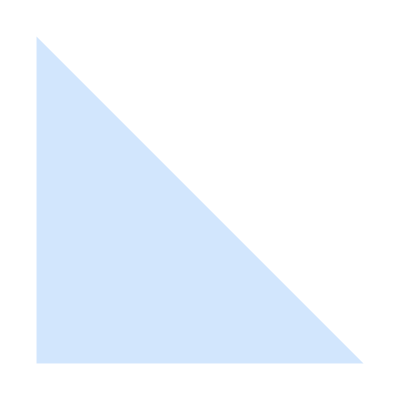
{a+b+4 c-d==9
a-c==1
a-2 b+4 c==6
2 a+3 c-3 d==8 | ⟶ | (1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
2 | 0 | 3 | -3 | 8) | ⟶ | -Graphics-(2 | 0 | 3 | -3 | 8
0 | -2 | 5/2 | 3/2 | 2
0 | 0 | 15/4 | 5/4 | 6
0 | 0 | 0 | 7/3 | 1)
Sistema lineare |  | Matrice completa associata |  | Matrice ridotta a gradini

Come ottenere gli zeri che vedi nella matrice ridotta a gradini?

```mathematica
gaussFirstString = {"Il metodo di Gauss è un procedimento ordinato di calcolo che permette la risoluzione di un sistema lineare\nmediante un numero finito di ", Style["step", Bold, FontSize-> 30]," attraverso l'uso di ", Style["matrici", Bold, FontSize-> 30],"."};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussThirdString = {"\nLo scopo è quello di ", Style["ridurre a gradini", Bold], " la matrice completa associata al sistema."};
gaussThirdString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussThirdString ];

linearSystem = {a+b+4c-d== 9, a-c== 1, a-2b+4c== 6, 2a+3c-3d== 8};
transformed = transformToMatrix[linearSystem, True];
matrix = highlightMatrixElements[transformed] // MatrixForm;
{L,U,P,newB}=fattorizzazioneLU[Drop[transformed,None,-1],Take[transformed,All,-1]];
upperMatrix = highlightMatrixElements[Join[U,ArrayReshape[newB,{Length[newB],1}],2]]//MatrixForm;
triangle = Triangle[{{0,0}, {0,4}, {4,0}}];
triangleMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.2], triangle}]}}, ItemSize-> 7, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,2}];
upperMatrix = Overlay[{triangleMatrix, upperMatrix}, All, 2];

thirdString = Style["Sistema lineare", Italic];
fourthString = Style["Matrice completa associata", Italic];
fifthString = Style["Matrice ridotta a gradini", Italic];

Grid[{{gaussFirstString}, {gaussThirdString}}, Frame -> None,ItemSize-> Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Framed[Grid[{{Grid[{{displayEquationSystem[linearSystem], "⟶", matrix, "⟶", upperMatrix}, {thirdString, "",fourthString, "",fifthString}}, Frame -> None,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings->{5,0}]}}, Frame->None, ItemSize->Fit], FrameStyle-> None, FrameMargins-> {{0,0}, {0,30}}]
Framed[Grid[{{"Come ottenere gli zeri che vedi nella matrice ridotta a gradini?"}}, Frame -> True, FrameStyle-> RGBColor[0.94,0.94,0.94],Background->RGBColor[1,0.8,0.4], ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24]], 
FrameStyle-> None, FrameMargins-> {{0,0}, {0,30}}]
```

### Metodo di Gauss

#### Le mosse

```mathematica
gaussFirstString = {"Ogni step può essere composto da una o più ", Style["«mosse»", Bold], " tra le seguenti:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussFirstString ];
gaussSecondString = {"• ",Style["MOSSA 1", Bold],": scambio di due righe della matrice."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussSecondString ];
gaussThirdString = {"• ", Style["MOSSA 2", Bold],": combinazione (lineare) di righe:\n  ",Style["Sostituire una riga della matrice con un’altra, ottenuta sottraendo ad essa\n  un’altra riga moltiplicata precedentemente per un numero diverso da zero.", FontSize->21]};
gaussThirdString = Apply[StringJoin, ToString[#, StandardForm] & /@ gaussThirdString ];

lookHerePlay1 = Hyperlink["Guarda qui", {"Home.nb", "Play1"}, BaseStyle -> RGBColor[0.2, 0.6, 0.86]];
lookHerePlay2 = Hyperlink["Guarda qui", {"Home.nb", "Play2"}, BaseStyle -> RGBColor[0.2, 0.6, 0.86]];
lookHerePlay1Grid = Grid[{{lookHerePlay1}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 30, FontWeight -> Bold]];
lookHerePlay2Grid = Grid[{{lookHerePlay2}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 30, FontWeight -> Bold]];

Grid[{{gaussFirstString}, {Framed[Grid[{{gaussSecondString , lookHerePlay1Grid}, {gaussThirdString, lookHerePlay2Grid}}, Frame -> None, Alignment -> {Left, Bottom}, Spacings -> {2, 1}], FrameStyle -> None, FrameMargins -> {{30, 0}, {0, 0}}]}}, Frame -> None, ItemStyle -> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment -> Left]
```

Ogni step può essere composto da una o più «mosse» tra le seguenti:
• MOSSA 1: scambio di due righe della matrice. | Guarda quiHome.nbPlay1Home.nbHyperlinkHyperlinkActive
• MOSSA 2: combinazione (lineare) di righe:
  Sostituire una riga della matrice con un’altra, ottenuta sottraendo ad essa
  un’altra riga moltiplicata precedentemente per un numero diverso da zero. | Guarda quiHome.nbPlay2Home.nbHyperlinkHyperlinkActive

### Metodo di Gauss

#### Mossa 1

```mathematica
myString1 = "Scambio di due righe della matrice:";
firstMatrix = {{1,4,0,6},{2,6,2,8},{0,3,-3,8}};
firstMatrix = MapAt[Style[#,Red]&,firstMatrix,{1,All}];
firstMatrix = MapAt[Style[#,RGBColor[1,0,1]]&,firstMatrix,{2,All}];
secondMatrix = Permute[firstMatrix, {2,1}]//MatrixForm;
firstMatrix = firstMatrix//MatrixForm;
(*firstMatrix = {{Style[1, Red],Style[4, Red],Style[0, Red],Style[6, Red]}, {Style[2, RGBColor[1,0,1]],Style[6, RGBColor[1,0,1]],Style[2, RGBColor[1,0,1]],Style[8, RGBColor[1,0,1]]}, {0,3,-3,8}} // MatrixForm;
secondMatrix = {{Style[2, RGBColor[1,0,1]],Style[6, RGBColor[1,0,1]],Style[2, RGBColor[1,0,1]],Style[8, RGBColor[1,0,1]]}, {Style[1, Red],Style[4, Red],Style[0, Red],Style[6, Red]},{0,3,-3,8}} // MatrixForm;*)
leftArrow = ImageResize[-Graphics-, 30];
rightArrow =ImageResize[-Graphics-, 30];
Grid[{{myString1}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
matrixGrid = Grid[{{leftArrow, firstMatrix, rightArrow}}, Frame-> None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Top];
rowsGrid = Grid[{{"R2 ↔ R1"}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, FontWeight-> Bold], Background-> RGBColor[0.13,0.52,0.96, 0.5]];
Grid[{{Grid[{{matrixGrid, rowsGrid, secondMatrix}}, Frame-> True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings-> {10,5}]}}, Frame->None, ItemSize->Fit]

myString = {"Ogni elemento della riga 2 (", Style["R2", Bold],") adesso è sulla riga 1 (", Style["R1", Bold],") e viceversa."};
myString = Apply[StringJoin, ToString[#, StandardForm] &/@ myString ];
Grid[{{myString}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Scambio di due righe della matrice:

-Graphics- | (1 | 4 | 0 | 6
2 | 6 | 2 | 8
0 | 3 | -3 | 8) | -Graphics- | R2 ↔ R1 | (2 | 6 | 2 | 8
1 | 4 | 0 | 6
0 | 3 | -3 | 8)

Ogni elemento della riga 2 (R2) adesso è sulla riga 1 (R1) e viceversa.

### Metodo di Gauss

#### Mossa 2

```mathematica
firstString = {"Sostituire una riga (",Style["R2",Bold],") della matrice con un’altra (",Style["nuova R2", Bold],"), ottenuta ",Style["sottraendo", Underlined] ," ad essa (",Style["R2",Bold],") un’altra riga (",Style["R1",Bold],") moltiplicata\nprecedentemente per un ",Style["numero diverso da zero", Bold,Red],".\n",Style["L’obiettivo è quello di ottenere degli zeri", Underlined],".\nEsempio: Vogliamo annullare l’elemento ",Framed[" 1 ", RoundingRadius-> 100, FrameStyle-> Orange]," sotto il pivot ", Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],"."};
firstString = Apply[StringJoin, ToString[#, StandardForm] &/@ firstString ];

rowSubstitution = ImageResize[-Graphics-, 600];
firstMatrix = {{Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],6,-2,9}, {Framed[" 1 ", RoundingRadius->100, FrameStyle->Orange],4,0,6}, {0,3,-3,8}} // MatrixForm;
secondMatrix = {{3,6,-2,9}, {1-HoldForm[3/3], 4-HoldForm[6/3], HoldForm[0] -HoldForm[-2/3]"", 6-HoldForm[9/3]}, {0,3,-3,8}} // MatrixForm;
thirdMatrix = {{Style[3, Bold, RGBColor[0.2, 0.6, 0.2]],6,-2,9}, {Framed[" 0 ", RoundingRadius->100, FrameStyle->Orange],3,2/3,3}, {0,3,-3,8}} // MatrixForm;

secondString = {"Il ", Style["numero diverso da zero", Bold,Red], " sarà: ", HoldForm[Style["elemento da annullare",Italic, FontSize->24]/Style["pivot",Italic, FontSize->24]]};
secondString = Apply[StringJoin, ToString[#, StandardForm] &/@ secondString ];

Grid[{{firstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
Grid[{{rowSubstitution}, {Grid[{{firstMatrix, "⟶", secondMatrix, "⟶", thirdMatrix}},Frame->None, Spacings->{3,0}]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Spacings->{0,4}] /. x_Image:>Image[x,Magnification->1]
Grid[{{secondString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

Sostituire una riga (R2) della matrice con un’altra (nuova R2), ottenuta sottraendo ad essa (R2) un’altra riga (R1) moltiplicata
precedentemente per un numero diverso da zero.
L’obiettivo è quello di ottenere degli zeri.
Esempio: Vogliamo annullare l’elemento  1  sotto il pivot 3.

-Graphics-
(3 | 6 | -2 | 9
 1  | 4 | 0 | 6
0 | 3 | -3 | 8) | ⟶ | (3 | 6 | -2 | 9
1-3/3 | 4-6/3 | 0- (-2/3) | 6-9/3
0 | 3 | -3 | 8) | ⟶ | (3 | 6 | -2 | 9
 0  | 3 | 2/3 | 3
0 | 3 | -3 | 8)

Il numero diverso da zero sarà: (elemento da annullare)/pivot

### Metodo di Gauss

#### Step 1 • Colonna 1

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

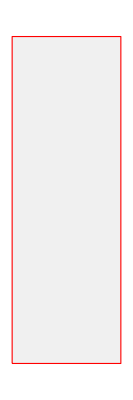
-Graphics-(1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
 2  | 0 | 3 | -3 | 8) | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.

Nota bene:
Il pivot non deve essere mai zero.
Se ci sono due pivot uguali in valore assoluto devi scegliere il primo che trovi scorrendo dall'alto verso il basso.

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la ", Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussSecondString = {"• Cerca per la prima colonna l'elemento massimo.\n  E' il ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_41."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussSecondString ];
thirdString = Style["Nota bene:", Bold, Red];
fourthString = {"Il pivot non deve essere mai zero.\nSe ci sono due pivot uguali in valore assoluto devi scegliere il " ,Style["primo", Bold, Underlined]," che trovi scorrendo dall'alto verso il basso."};
fourthString = Apply[StringJoin, ToString[#, StandardForm] &/@ fourthString ];

matrix = {{1,1,4,-1,9}, {1,0,-1,0,1}, {1,-2,4,0,6}, {Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8}} // MatrixForm;
rectangle = Rectangle[{0,0},{0.5,1.5}];
rectangleMatrix = Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings-> {0.6,0}];
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{designedMatrix, gaussSecondString}}, Frame->True,FrameStyle -> RGBColor[0.94,0.94,0.94],ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,5}]
Grid[{{thirdString}, {fourthString}}, Frame->None,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Left]
```

### Metodo di Gauss

#### Step 1 • Colonna 1

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la " ,Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];
gaussSecondString = {"• Cerca per la prima colonna l'elemento massimo.\n  E' il ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_41.\n• Scambia la prima riga con la quarta.\n  In modo da ottenere ", Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_11."};
gaussSecondString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussSecondString ];
leftArrow = ImageResize[-Graphics-, {60,150}];
rightArrow =ImageResize[-Graphics-, {60,150}];
swapRows  = ImageResize[-Graphics-, 400];
matrix = {{1,1,4,-1,9}, {1,0,-1,0,1}, {1,-2,4,0,6}, {Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8}} // MatrixForm;
rectangle = Rectangle[{0,0},{0.5,1.5}];
rectangleMatrix = Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings-> {0.6,0}];
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{Grid[{{leftArrow, designedMatrix, rightArrow}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment->Top], gaussSecondString},{"", swapRows}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,4}]
```

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

-Graphics- | -Graphics-(1 | 1 | 4 | -1 | 9
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
 2  | 0 | 3 | -3 | 8) | -Graphics- | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.
• Scambia la prima riga con la quarta.
  In modo da ottenere  2  in posizione a_11.
 | -Graphics-

### Metodo di Gauss

#### Step 1 • Colonna 1

```mathematica
gaussFirstString = {"È necessario operare sulla matrice con la " ,Style["MOSSA 1", Bold]," dello ", Style["scambio di righe", Bold], "\nin modo da scegliere come ", Style["pivot ", Bold, RGBColor[0.2, 0.6, 0.2]],Style["l’elemento massimo in valore assoluto", Bold, Underlined],".\nAd esempio:"};
gaussFirstString = Apply[StringJoin, ToString[#, StandardForm] &/@ gaussFirstString ];

matrix = {{Framed[" 2 ", RoundingRadius-> 100, FrameStyle-> Orange],0,3,-3,8},{1,0,-1,0,1}, {1,-2,4,0,6}, {1,1,4,-1,9}} // MatrixForm;
designedMatrix = Overlay[{rectangleMatrix, Framed[matrix, FrameStyle-> None, FrameMargins->{{0,0}, {0,8}}]}, All, 2];

Grid[{{gaussFirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left]
Grid[{{designedMatrix, gaussSecondString}, {"", swapRows}}, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94],ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}, Spacings->{0,4}]
```

È necessario operare sulla matrice con la MOSSA 1 dello scambio di righe
in modo da scegliere come pivot l’elemento massimo in valore assoluto.
Ad esempio:

-Graphics-( 2  | 0 | 3 | -3 | 8
1 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | • Cerca per la prima colonna l'elemento massimo.
  E' il  2  in posizione a_41.
• Scambia la prima riga con la quarta.
  In modo da ottenere  2  in posizione a_11.
 | -Graphics-

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 2

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["primo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_2 : R_2 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-1,0,1}, {1,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,2],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{Range[3,4],Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{2,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[0, Red];
blue1 = Style[-1, Blue];
blue2 = Style[3, Blue];
purple2= Style[-3, RGBColor[1,0,1]];
purple1 = Style[0, RGBColor[1,0,1]];
lightBlue2 = Style[8, RGBColor[0.13,0.52,0.96]];
lightBlue1 = Style[-3,RGBColor[0.13,0.52,0.96]];

firstOperation = {"0 - ", normalOne /pivotTwo," * 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"-1 - ",normalOne/pivotTwo," * 3 = ",Style["-",Blue],Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"0 - ",normalOne/pivotTwo," * (-3) = ",Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"1 - ",normalOne/pivotTwo," * 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];
fifthOperation = {normalOne," - ",normalOne/pivotTwo," * ",pivotTwo," = ",Framed[0, FrameStyle->Orange]};
fifthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fifthOperation];

matrixStep3 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {1,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep3 = MapAt[Style[#, Red]&,matrixStep3,{{1,2},{2,2}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,2}}];
finalMatrixStep3 = MapAt[Style[#, Blue]&,finalMatrixStep3,{{1,3},{2,3}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,3}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[1,0,1]]&,finalMatrixStep3,{{1,4},{2,4}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,4}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalMatrixStep3,{{1,5},{2,5}}];
finalMatrixStep3 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalMatrixStep3,{{2,5}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep3,{{2,1}}];
finalMatrixStep3 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalMatrixStep3,{{1,1}}];
finalMatrixStep3 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep3,{{Range[3,4],Range[1,5]}}];
finalMatrixStep3 = finalMatrixStep3 // MatrixForm;
rightArrow = ImageResize[-Graphics-,100];
elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Center];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalMatrixStep3}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Spacings->{3,4}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{5,0} ];
Grid[{{step2FirstString},{Grid[{{matrixGrid}},ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il primo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -1 | 0 | 1
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_2 : R_2 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
1 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9)
1 - 1/2 * 2 = 0 | 0 - 1/2 * 0 = 0 | -1 - 1/2 * 3 = -5/2 | 0 - 1/2 * (-3) = 3/2 | 1 - 1/2 * 8 = -3

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 3

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["secondo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_3 : R_3 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,4,0,6}, {1,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,2],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{3,Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalMatrixStep2,{{4,Range[1,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{3,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[-2, Red];
lightBlue1 = Style[2,RGBColor[0.13,0.52,0.96]];
firstOperation = {"-2 - ", normalOne /pivotTwo," * 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"4 - ",normalOne/pivotTwo," * 3 = ",Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"0 - ",normalOne/pivotTwo," * (-3) = ",Style[3, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"6 - ",normalOne/pivotTwo," * 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {1,1,4,-1,9}};
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{1,2},{3,2}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,2}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{1,3},{3,3}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[1,0,1]]&,finalSecondMatrixStep2,{{1,4},{3,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalSecondMatrixStep2,{{1,5},{3,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{3,5}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{2,1}}];
finalSecondMatrixStep2= MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{1,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{2,Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{3,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,Range[1,5]}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;

elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{5,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il secondo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 4 | 0 | 6
1 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_3 : R_3 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
1 | 1 | 4 | -1 | 9)
1 - 1/2 * 2 = 0 | -2 - 1/2 * 0 = -2 | 4 - 1/2 * 3 = 5/2 | 0 - 1/2 * (-3) = 3/2 | 6 - 1/2 * 8 = 2

### Metodo di Gauss

#### Step 2 • Colonna 1, Riga 4

```mathematica
normalOne = Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24];
pivotTwo = Style[2, Bold,RGBColor[0.2,0.6,0.2], FontFamily->"Roboto Condensed",FontSize->24];
step2FirstString = {"Rendere nullo il ", Style["terzo elemento", Orange] ," sotto il ",Style["pivot a_11 = 2", Bold , RGBColor[0.2, 0.6, 0.2]]," ed effettuare la ",Style["MOSSA 2", Bold]," per ",Style["tutti", Bold,Underlined], " gli elementi della ",Style["stessa", Bold] ," riga."};
step2FirstString = Apply[StringJoin, ToString[#, StandardForm] & /@ step2FirstString];
step3SecondString = {Style["MOSSA 2",Bold],"\nnuova R_4 : R_4 - ",normalOne/pivotTwo," R_1"};
step3SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step3SecondString];

matrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {0,1,4,-1,9}};
finalMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,matrixStep2,{{Range[1,4],Range[2,5]}}];
finalMatrixStep2 = MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2]]&,finalMatrixStep2,{{1,1}}];
finalMatrixStep2 = MapAt[Framed[#, FrameStyle->Orange]&,finalMatrixStep2,{{4,1}}];
finalMatrixStep2 = finalMatrixStep2 // MatrixForm;

red1 = Style[1, Red];
lightBlue1 = Style[5,RGBColor[0.13,0.52,0.96]];
firstOperation = {"1 - ", normalOne /pivotTwo," * 0 = ", red1};
firstOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ firstOperation];
secondOperation = {"4 - ",normalOne/pivotTwo," * 3 = ",Style[5, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, Blue]};
secondOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ secondOperation];
thirdOperation = {"-1 - ",normalOne/pivotTwo," * (-3) = ",Style[1, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]/Style[2, FontFamily -> "Roboto Condensed", FontSize-> 24, RGBColor[1,0,1]]};
thirdOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ thirdOperation];
fourthOperation = {"9 - ",normalOne/pivotTwo," * 8 = ",lightBlue1};
fourthOperation = Apply[StringJoin, ToString[#, StandardForm] & /@ fourthOperation];

thirdMatrixStep2 = {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,-2,5/2,3/2,2}, {0,1,5/2,1/2,5}};
finalSecondMatrixStep2 = MapAt[Style[#, Red]&,thirdMatrixStep2,{{1,2},{4,2}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,2}}];
finalSecondMatrixStep2 = MapAt[Style[#, Blue]&,finalSecondMatrixStep2,{{1,3},{4,3}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,3}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[1,0,1]]&,finalSecondMatrixStep2,{{1,4},{4,4}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,4}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0.13,0.52,0.96]]&,finalSecondMatrixStep2,{{1,5},{4,5}}];
finalSecondMatrixStep2 = MapAt[Framed[#, RoundingRadius->100,FrameStyle->Orange]&,finalSecondMatrixStep2,{{4,5}}];
finalSecondMatrixStep2= MapAt[Style[#, Bold,RGBColor[0.2,0.6,0.2,0.4]]&,finalSecondMatrixStep2,{{1,1}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{Range[2,3],Range[1,5]}}];
finalSecondMatrixStep2 = MapAt[Style[#, RGBColor[0,0,0,0.4]]&,finalSecondMatrixStep2,{{4,1}}];
finalSecondMatrixStep2 = finalSecondMatrixStep2// MatrixForm;

elementsGrid = Grid[{{step3SecondString},{rightArrow}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24, TextAlignment-> Center], Alignment->{Center, Center}];
matrixGrid = Grid[{{finalMatrixStep2, elementsGrid, finalSecondMatrixStep2}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Spacings->{3,5}];
operationsGrid = Grid[{{fifthOperation,firstOperation,secondOperation,thirdOperation,fourthOperation}},Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94], 
ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24],Spacings->{5,0} ];
Grid[{{step2FirstString}, {Grid[{{matrixGrid}}, ItemSize->Fit]},{Grid[{{operationsGrid}},ItemSize->Fit]}}, Frame->True,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle->Directive[FontFamily -> "Roboto Condensed", FontSize-> 24], Alignment->Left]
```

Rendere nullo il terzo elemento sotto il pivot a_11 = 2 ed effettuare la MOSSA 2 per tutti gli elementi della stessa riga.
(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 4 | -1 | 9) | MOSSA 2
nuova R_4 : R_4 - 1/2 R_1
-Graphics- | (2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 5/2 | 1/2 | 5)
1 - 1/2 * 2 = 0 | 1 - 1/2 * 0 = 1 | 4 - 1/2 * 3 = 5/2 | -1 - 1/2 * (-3) = 1/2 | 9 - 1/2 * 8 = 5

### Metodo di Gauss

#### Step 1 • Colonna 2

A questo punto tutti gli elementi sotto il pivot a_11 sono nulli (zero).
Ora prendiamo in considerazione la posizione a_22 e gli elementi al di sotto di esso.
Qual è l’elemento massimo in valore assoluto tra questi?
È il -2 in posizione a_32.

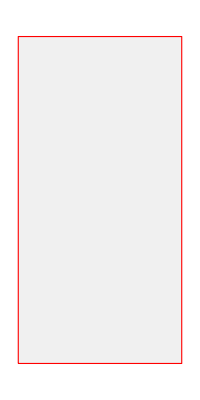
-Graphics- | -Graphics-(2 | 0 | 3 | -3 | 8
0 | 0 | -5/2 | 3/2 | -3
0 | -2 | 5/2 | 3/2 | 2
0 | 1 | 5/2 | 1/2 | 5) | -Graphics- | • Scambia la seconda riga con la terza.
  In modo da ottenere -2 in posizione a_22.
 | -Graphics-

```mathematica
step1FirstString = {"A questo punto tutti gli elementi sotto il ",Style["pivot a_11", Bold, RGBColor[0.2,0.6,0.2]]," sono nulli (",Style["zero",Bold],").\nOra prendiamo in considerazione la posizione a_22 e gli elementi al di ", Style["sotto",Bold] ," di esso.\nQual è ",Style["l’elemento massimo in valore assoluto", Bold, Underlined] ," tra questi?\nÈ il ",Framed["-2", RoundingRadius->100, FrameStyle->Orange] ," in posizione a_32."};
step1FirstString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1FirstString];
step1SecondString = {"• Scambia la seconda riga con la terza.\n  In modo da ottenere ", Framed["-2", RoundingRadius-> 100, FrameStyle-> Orange], " in posizione a_22."};
step1SecondString =  Apply[StringJoin, ToString[#, StandardForm] & /@ step1SecondString];
leftArrow = ImageResize[-Graphics-, {40,70}];
rightArrow =ImageResize[-Graphics-, {40,70}];
swapRows = ImageResize[-Graphics-,400];
matrixStep1= {{2,0,3,-3,8},{0,0,-5/2,3/2,-3}, {0,Framed["-2", RoundingRadius->100, FrameStyle->Orange],5/2,3/2,2}, {0,1,5/2,1/2,5}} // MatrixForm;
rectangle = Rectangle[{0,0},{1,2}];
rectangleMatrix = Framed[Grid[{{Graphics[{EdgeForm[{Thick, Red}],RGBColor[0.94, 0.94, 0.94], rectangle}]}}, ItemSize->3.5, Frame -> True,FrameStyle->RGBColor[0.94,0.94,0.94], Spacings-> {2.5,0}], FrameStyle->None,FrameMargins->{{0,0},{0,33}}];
designedMatrix = Overlay[{rectangleMatrix, matrixStep1}, All, 2];

Framed[Grid[{{step1FirstString}}, Frame->None, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24],Alignment->Left], FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
matrixGrid = Grid[{{leftArrow, designedMatrix, rightArrow}}, Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24]];
Framed[Grid[{{matrixGrid,step1SecondString},{"", swapRows}}, Frame->None, ItemSize->Fit,ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24], Alignment-> {Center, Center}],FrameStyle->None, FrameMargins->{{0,0},{30,0}}]
```

### Esercizi

#### TODO: In questa slides fare un elenco cliccabile dei vari esercizi possibili

### Prova Tu: da sistema lineare a matrice

#### Guarda il sistema lineare che ti viene presentato e prova ad inserire i relativi coefficienti e termini noti nella matrice a fianco. Quando sei pronto, clicca su “Verifica!” per controllare il risultato oppure clicca su “Ricomincia” per provare con un altro sistema.

```mathematica
exerciseSystemToMatrix[]
```

```mathematica
exerciseTag= "";
backTag = "MatriciPag1";
backButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb",backTag}];
backLink := Hyperlink["Torna alla Teoria", {"Home.nb", backTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
exerciseBackLink := Hyperlink["Torna agli Esercizi", {"Home.nb", exerciseTag}, BaseStyle->RGBColor[0.2,0.6,0.86]];
navEsercizi := Grid[{{exerciseButton, exerciseBackLink,backLink,backButton}},Alignment->{{Right,Left,Right,Left}}, ItemSize->{{Scaled[0.08],Scaled[0.42],Scaled[0.42],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navEsercizi
Clear[backTag];
```

-Graphics-Home.nbHome.nb | Torna agli EserciziHome.nbHome.nbHyperlinkHyperlinkActive | Torna alla TeoriaHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag1Home.nb

### Prova Tu: Domande sulla Teoria

```mathematica
exerciseMatrix[]
```

### Prova Tu: Sistema associato alla matrice ridotta

#### Partendo dalla matrice ridotta usando gli step e le mosse di Gauss, scrivi ogni equazione del sistema associato

RICORDA: La matrice è completa e sono evidenziati i coefficienti (blu) ed i termini noti (verde)!

```mathematica
exerciseReducedMatrixToSystem[]
```

### Prova Tu: Metodo di Gauss

#### Rendi questa matrice a gradini attraverso gli step e usando le mosse di Gauss che hai visto nella teoria.

RICORDA: La matrice è completa e sono evidenziati i coefficienti (blu) ed i termini noti (verde)!

```mathematica
exerciseTriangularizeMatrix[getRandomSystem[]]
```

### Mani all’opera!

#### Scrivere sottotitolo QUI!